```mathematica
params=Import["/home/tatjam/code/tfg/workdir/theodorsen_params.dat"];
liftTime=Import["/home/tatjam/code/tfg/workdir/theodorsen_lift_over_time.dat"][[1]];
liftTimeSteady=Import["/home/tatjam/code/tfg/workdir/theodorsen_lift_over_time_steady.dat"][[1]];
```

```mathematica
longTerm=Import["/home/tatjam/code/tfg/workdir/theodorsen_long_term_forces.dat"][[1]];
```

```mathematica
offset=params[[3]][[1]];
```

```mathematica
ts=Table[params[[2]][[1]]*i, {i, offset,2*offset-1}]; (* Tiempos dimensionales *)
heaveampl=params[[4]][[1]];
ω=params[[5]][[1]];
AoA=heaveampl*Sin[ω*ts];
vel=params[[1]][[1]];
chord=0.25;
tadim=ts*vel/chord;
```

Lift ideal generado por el perfil, vs lift según el método de paneles

```mathematica
ideal=2π*0.1;
```

```mathematica
real=longTerm[[2]]/chord;
```

Obtenemos el factor de correción ϵ

```mathematica
ϵ=ideal/real
```

1.26449

Valor de la frecuencia reducida

```mathematica
k=(ω*chord)/(2*vel)
```

0.125

```mathematica
besselH0[k_]:=BesselJ[0,k]-I*BesselY[0,k];
```

```mathematica
besselH1[k_]:=BesselJ[1,k]-I*BesselY[1,k];
```

```mathematica
theodorsenLag[k_]=besselH1[k]/(besselH1[k]+I*besselH0[k]);
```

Esperamos un desfase de...

```mathematica
Arg[theodorsenLag[k]]*180/π
```

-12.7783

Máximo desplazamiento respecto a la posición inicial por el “heaving”

```mathematica
hampl=vel* heaveampl/ω;
hampl
```

0.06

Funciones para teoría de Theodorsen

```mathematica
clQ:=2π*AoA;
clA:=2π*(-k*k*hampl/chord)*Exp[I*ω*ts]
```

```mathematica
cls:=Re[theodorsenLag[k]*clQ+clA];
```

Función que permite combinar datos brutos y los tiempos adimensionales

```mathematica
dataWithTime[data_,time_]:=
Thread[{#2,#1}&[data,time]]
```

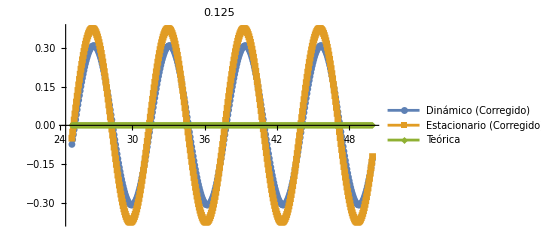

```mathematica
ListLinePlot[{
dataWithTime[liftTime/chord*ϵ,ts],
dataWithTime[liftTimeSteady/chord*ϵ,ts],
dataWithTime[cls*0,ts]},
PlotLegends->{"Dinámico (Corregido)", "Estacionario (Corregido)","Teórica"},PlotRange->{All,All},PlotMarkers->{Automatic, 7},
PlotLabel->k]
```

```mathematica
alphaOverTime=Import["/home/tatjam/code/tfg/workdir/theodorsen_alpha_over_time.dat"][[1]];
```

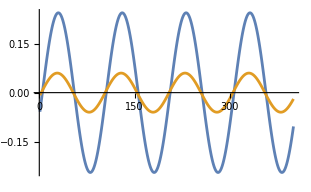

```mathematica
ListLinePlot[{liftTime/chord,alphaOverTime}]
```

FittedModel[1.96219×10^-7-0.0612266 Sin[0.107819-x]]

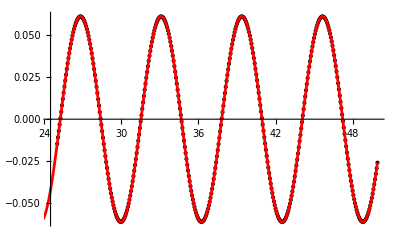

```mathematica
nlmDynamic=NonlinearModelFit[dataWithTime[liftTime,ts],a+b*Sin[x+c],{a,b,c},x]
nlmDynamic["BestFitParameters"];
Show[ListPlot[dataWithTime[liftTime,ts],PlotStyle->Black],Plot[nlmDynamic[x],{x,0,ts[[-1]]},PlotStyle->Red]]
```

FittedModel[2.20373×10^-7+0.0743995 Sin[5.67845×10^-6+x]]

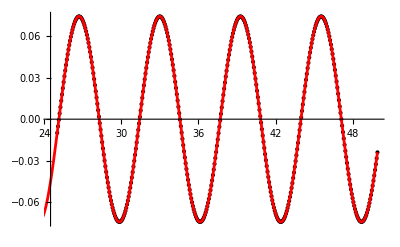

```mathematica
nlmStatic=NonlinearModelFit[dataWithTime[liftTimeSteady,ts],a+b*Sin[x+c],{a,b,c},x]
nlmStatic["BestFitParameters"];
Show[ListPlot[dataWithTime[liftTimeSteady,ts],PlotStyle->Black],Plot[nlmStatic[x],{x,0,ts[[-1]]},PlotStyle->Red]]
```

```mathematica
phaseOffset=(c/.nlmStatic["BestFitParameters"])-(c/.nlmDynamic["BestFitParameters"])
```

```mathematica
0.107825
```

```mathematica
gainRelation=(b/.nlmDynamic["BestFitParameters"])/(b/.nlmStatic["BestFitParameters"])
```

0.822943

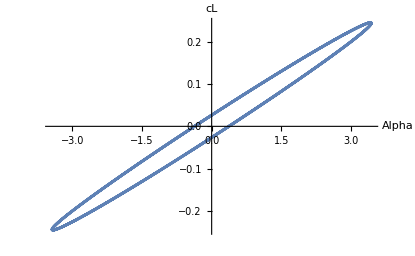

```mathematica
ListLinePlot[dataWithTime[liftTime/chord,alphaOverTime*180/π],AxesLabel->{"Alpha", "cL"}]
```

Obtención del desfase entre estacionario y dinámico

```mathematica
maximoDinamicoTadim=ts[[Ordering[Take[liftTime,28],-1]]]
```

{26.6875}

```mathematica
maximoEstacionarioTadim=ts[[Ordering[Take[liftTimeSteady,28],-1]]]
```

{26.6875}

```mathematica
maximoWagnerTadim=ts[[Ordering[Take[cls,28],-1]]]
```

{26.6875}

```mathematica
desfaseWagnerTiempo=maximoWagnerTadim[[1]]-maximoEstacionarioTadim[[1]]
```

0.

```mathematica
desfaseWagnerAngulo=desfaseWagnerTiempo*ω*180/π
```

0.

```mathematica
desfaseDinamicoTiempo=maximoDinamicoTadim[[1]]-maximoEstacionarioTadim[[1]]
```

0.

```mathematica
desfaseDinamicoAngulo=desfaseDinamicoTiempo*ω*180/π
```

0.